# Similarity Index of 1D Cellular Automata

## Graph approach

Erick Jesse Angeles Lopez

### Graph of space evolution

In a space with 4 cells, we have  possible spaces. Each of one can be represented as a node and be connected by a rule:

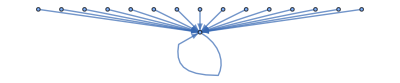
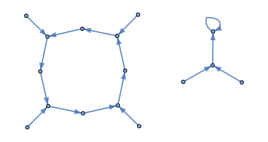
0_(2,3) | 31_(2,3) | 62_(2,3)
-Graphics- | -Graphics- | -Graphics-

But we can compare both graphs, because they can have the same shape but no the same nodes:

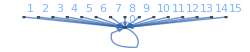
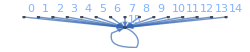
0_(2,3) | 255_(2,3)
-Graphics- | -Graphics-

We can test if they are isomorphic, that means, there is a bijective function that maps each vertex in the transition matrix

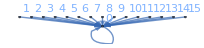
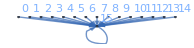
```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

True

We can obtain the canonical form of this graphs. There is not an specific algorithm:

Calculate the degree of each node and en-queue the leaf nodes.

For each leaf node, assign a structural code for the parent.

en-queue the parent node if now it is a leaf.

Find cicles and asssing codes

Differences with grouping by mirror and state permutatation:

{15_(2,3),85_(2,3),170_(2,3),240_(2,3)} | {{15_(2,3),85_(2,3)},{240_(2,3),170_(2,3)}}
{23_(2,3),178_(2,3)} | {{23_(2,3)},{178_(2,3)}}
{25_(2,3),45_(2,3),61_(2,3),67_(2,3),75_(2,3),89_(2,3),101_(2,3),103_(2,3)} | {{45_(2,3),75_(2,3),101_(2,3),89_(2,3)},{67_(2,3),61_(2,3),25_(2,3),103_(2,3)}}
{28_(2,3),70_(2,3),78_(2,3),92_(2,3),141_(2,3),157_(2,3),197_(2,3),199_(2,3)} | {{28_(2,3),199_(2,3),70_(2,3),157_(2,3)},{78_(2,3),141_(2,3),92_(2,3),197_(2,3)}}
{77_(2,3),232_(2,3)} | {{77_(2,3)},{232_(2,3)}}
{105_(2,3),150_(2,3)} | {{105_(2,3)},{150_(2,3)}}

The mirror and state permutation have the same isomorphic graph. But here comes the next question: What should be the size of the space?

Because if we considered a single cell, we have only 3 behaviors:

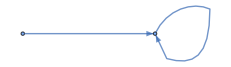
0_(2,3) | 1_(2,3) | 128_(2,3)
-Graphics- | -Graphics- | -Graphics-

Relation between the space size and the unique behaviors:

If we increase the space size we find similarities between 24 rules, but none of them are consistent belong the space size.

```mathematica
Meassure the similarity
```

To measure the similarity between rules. We obtain the cosine distances between the eigen values of each transition matrix:

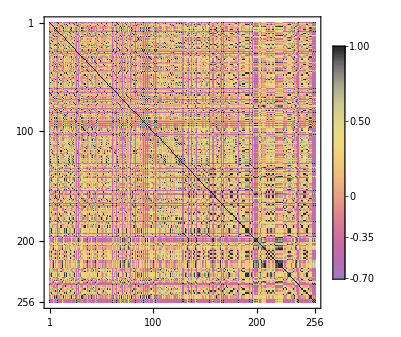

Similarity matrix for the unique behaviors:

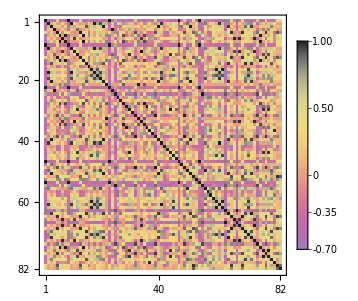

All distances between the mirror and inverse rule sets are zero; that is, they are equivalent with respect to the eigenvalues of the transition matrix in a state space of size 4.

# Thanks